# SIConstantConvert

Transform a unit into a product of constants

## Definition

```mathematica
ClearAll[SIConstantConvert]
SetAttributes[SIConstantConvert,Listable];
SIConstantConvert[unit_?QuantityQ]:=Block[{assoc,canonicalassoc,canonicalvector,HYPERFINETRANSITIONFREQUENCYOFCAESIUM,SPEEDOFLIGHTINVACUUM,PLANCKCONSTANT,ELEMENTARYCHARGE,BOLTZMANNCONSTANT,AVOGADROCONSTANT,LUMINOUSEFFICACYMONOCHROMATICRADIATION,DEFININGCONSTANTS,SIEXACTCONSTANTS,angleprocessedunit},angleprocessedunit=UnitSimplify[unit,UnityDimensions->Automatic];assoc=Association[Rule@@@UnitDimensions[angleprocessedunit]];canonicalassoc=Append[Association["TimeUnit"->0,"LengthUnit"->0,"MassUnit"->0,"ElectricCurrentUnit"->0,"TemperatureUnit"->0,"AmountUnit"->0,"LuminousIntensityUnit"->0],assoc];canonicalvector={canonicalassoc["TimeUnit"],canonicalassoc["LengthUnit"],canonicalassoc["MassUnit"],canonicalassoc["ElectricCurrentUnit"],canonicalassoc["TemperatureUnit"],canonicalassoc["AmountUnit"],canonicalassoc["LuminousIntensityUnit"]};HYPERFINETRANSITIONFREQUENCYOFCAESIUM={-1,0,0,0,0,0,0};SPEEDOFLIGHTINVACUUM={-1,1,0,0,0,0,0};PLANCKCONSTANT={-1,2,1,0,0,0,0};ELEMENTARYCHARGE={1,0,0,1,0,0,0};BOLTZMANNCONSTANT={-2,2,1,0,-1,0,0};AVOGADROCONSTANT={0,0,0,0,0,-1,0};LUMINOUSEFFICACYMONOCHROMATICRADIATION={3,-2,-1,0,0,0,1};DEFININGCONSTANTS={HYPERFINETRANSITIONFREQUENCYOFCAESIUM,SPEEDOFLIGHTINVACUUM,PLANCKCONSTANT,ELEMENTARYCHARGE,BOLTZMANNCONSTANT,AVOGADROCONSTANT,LUMINOUSEFFICACYMONOCHROMATICRADIATION};SIEXACTCONSTANTS={Quantity["Cesium133HyperfineSplittingFrequency"],Quantity["SpeedOfLight"],Quantity["PlanckConstant"],Quantity["ElementaryCharge"],Quantity["BoltzmannConstant"],Quantity["AvogadroConstant"],UnitSimplify[Quantity["MonochromaticRadiation540THzLuminousEfficacy"],UnityDimensions->Automatic]};
UnitConvert[angleprocessedunit,Times@@Power@@@Transpose[{SIEXACTCONSTANTS,LinearSolve[Transpose[DEFININGCONSTANTS],canonicalvector]}]]]
SIConstantConvert[dist_]:=UnitConvert[dist,QuantityUnit[SIConstantConvert[Quantity[QuantityUnit[dist]]]]]/;Head[dist]==QuantityDistribution
```

## Documentation

### Usage

SIConstantConvert[unit]

transforms unit into a product of the seven SI defining constants.

### Details & Options

It would be helpful to explain what the seven defining constants of SI are. Or provide a link.

The defining constants are available in the BIPM’s SI Brochure and NIST's SI Brochure.

Defining the SI base units in terms of physical constants enables realizing the units with an accuracy that is limited only by the quantum structure of nature and our technical abilities but not by the definitions themselves.

The seven defining constants for the second, meter, kilogram, ampere, kelvin, mole, and candela are the hyperfine transition frequency of cesium-133, the speed of light in vacuum, the Planck constant, the Boltzmann constant, the Avogadro constant, and the the luminous efficacy of monochromatic radiation of frequency 540 × 10^12 hertz, respectively.

## Examples

### Basic Examples

Please start with a very simple first example like 

"[◼]" | "SIConstantConvert" [10 "m"]
1 "c""/""Δν"("("("")^133"Cs"")")_("hfs")

Convert the height of the Empire State building to a combination of physical constants:

```mathematica
SIConstantConvert[Entity["Building","EmpireStateBuilding::h583b"][EntityProperty["Building","Height"]]]
```

11682.7 c/Δν(^133Cs)_hfs

Transform the seven SI base units into products of constants:

Please avoid all caps symbols names in the examples. By convention this could be something like siBaseUnits.

I used SIBaseUnits because SI should not be spelled sI. SI stands for Système International in French or International System of Units in English.

```mathematica
SIBaseUnits=AssociationThread[{"time","length","mass","electric-current","thermodynamic-temperature","amount-of-substance","luminous-intensity"},{Quantity["Seconds"],Quantity["Meters"],Quantity["Kilograms"],Quantity["Amperes"],Quantity["Kelvins"],Quantity["Moles"],Quantity["Candelas"]}]
```

<|time→1 s,length→1 m,mass→1 kg,electric-current→1 A,thermodynamic-temperature→1 K,amount-of-substance→1 mol,luminous-intensity→1 cd|>

```mathematica
{#,SIConstantConvert[#],N[SIConstantConvert[#]]}&/@SIBaseUnits
```

<|time→{1 s,9192631770 /Δν(^133Cs)_hfs,9.19263×10^9 /Δν(^133Cs)_hfs},length→{1 m,656616555/21413747 c/Δν(^133Cs)_hfs,30.6633 c/Δν(^133Cs)_hfs},mass→{1 kg,36683884846400720000000000000000000000000000000000000000/2486164202903619 Δν(^133Cs)_hfs h/c^2,1.47552×10^40 Δν(^133Cs)_hfs h/c^2},electric-current→{1 A,500000000000000000000000000/736410991343003109 Δν(^133Cs)_hfs e,6.78969×10^8 Δν(^133Cs)_hfs e},thermodynamic-temperature→{1 K,276129800000000000/121822045942277331 Δν(^133Cs)_hfs h/k,2.26667 Δν(^133Cs)_hfs h/k},amount-of-substance→{1 mol,602214076000000000000000 /N_A,6.02214×10^23 /N_A},luminous-intensity→{1 cd,2000000000000000000000000000000000000000/76486793830390329632626020921 (Δν(^133Cs)_hfs)^2 K_cd h/rad^2,2.61483×10^10 (Δν(^133Cs)_hfs)^2 K_cd h/rad^2}|>

Please insert delimiters between independent examples using the button in the toolbar

This example is not "Basic" please move it into applications or properties and relations. It would also be easier to understand if you split it up or showed fewer values.

### Applications

Transform the 22 SI derived units with special names to products of constants:

```mathematica
siDerivedUnitsWithSpecialNames=AssociationThread[{"plane-angle","solid-angle","frequency","force","pressure-stress","energy-work-amount-of-heat","power-radiant-flux","electric-charge","electric-potential-difference","capacitance","electric-resistance","electric-conductance","magnetic-flux","magnetic-flux-density","inductance","Celsius-temperature","luminous-flux","illuminance","activity-referred-to-a-radionuclide","absorbed-dose-kerma","dose-equivalent","catalytic-activity"},{Quantity["Radians"],Quantity["Steradians"],Quantity["Hertz"],Quantity["Newtons"],Quantity["Pascals"],Quantity["Joules"],Quantity["Watts"],Quantity["Coulombs"],Quantity["Volt"],Quantity["Farads"],Quantity["Ohm"],Quantity["Siemens"],Quantity["Weber"],Quantity["Teslas"],Quantity["Henry"],Quantity["DegreesCelsius"],Quantity["Lumen"],Quantity["Lux"],Quantity["Becquerels"],Quantity["Gray"],Quantity["Sieverts"],Quantity["Katals"]}]
```

<|plane-angle→1 rad,solid-angle→1 sr,frequency→1 Hz,force→1 N,pressure-stress→1 Pa,energy-work-amount-of-heat→1 J,power-radiant-flux→1 W,electric-charge→1 C,electric-potential-difference→1 V,capacitance→1 F,electric-resistance→1 Ω,electric-conductance→1 S,magnetic-flux→1 Wb,magnetic-flux-density→1 T,inductance→1 H,Celsius-temperature→1 °C,luminous-flux→1 lm,illuminance→1 lx,activity-referred-to-a-radionuclide→1 Bq,absorbed-dose-kerma→1 Gy,dose-equivalent→1 Sv,catalytic-activity→1 kat|>

```mathematica
{#,SIConstantConvert[#],N[SIConstantConvert[#]]}&/@SIDERIVEDUNITSWITHSPECIALNAMES
```

<|plane-angle→{1 rad,1,1.},solid-angle→{1 sr,1,1.},frequency→{1 Hz,1/9192631770 Δν(^133Cs)_hfs,1.08783×10^-10 Δν(^133Cs)_hfs},force→{1 N,85654988000000000000000000000000000000000000000/15998074425933973987162941 (Δν(^133Cs)_hfs)^2 h/c,5.35408×10^21 (Δν(^133Cs)_hfs)^2 h/c},pressure-stress→{1 Pa,1571078858155917757395680000000000000000000000000000000000000/275899784103685663667223148042266362362461 (Δν(^133Cs)_hfs)^4 h/c^3,5.69438×10^18 (Δν(^133Cs)_hfs)^4 h/c^3},energy-work-amount-of-heat→{1 J,20000000000000000000000000000000000000000/121822045942277331 Δν(^133Cs)_hfs h,1.64174×10^23 Δν(^133Cs)_hfs h},power-radiant-flux→{1 W,2000000000000000000000000000000000000000/111986520981537817910140587 (Δν(^133Cs)_hfs)^2 h,1.78593×10^13 (Δν(^133Cs)_hfs)^2 h},electric-charge→{1 C,5000000000000000000000000000/801088317 e,6.24151×10^18 e},electric-potential-difference→{1 V,356039252000000000000/13535782882475259 Δν(^133Cs)_hfs h/e,26303.6 Δν(^133Cs)_hfs h/e},capacitance→{1 F,5639909534364691250000000000000/23768240430884907 e^2/(Δν(^133Cs)_hfs h),2.37288×10^14 e^2/(Δν(^133Cs)_hfs h)},electric-resistance→{1 Ω,213914163877964163/5521725125000000000000 h/e^2,0.0000387405 h/e^2},electric-conductance→{1 S,5521725125000000000000/213914163877964163 e^2/h,25812.8 e^2/h},magnetic-flux→{1 Wb,10681177560000000000000/44173801 h/e,2.41799×10^14 h/e},magnetic-flux-density→{1 T,65304514605833236205307200000000000/253937689300539269637507 (Δν(^133Cs)_hfs)^2 h/(e c^2),2.57167×10^11 (Δν(^133Cs)_hfs)^2 h/(e c^2)},inductance→{1 H,28091916270250853824503693/78881787500000000000 h/(Δν(^133Cs)_hfs e^2),356127. h/(Δν(^133Cs)_hfs e^2)},Celsius-temperature→{1 °C,75700984670000000000/121822045942277331 Δν(^133Cs)_hfs h/k,621.406 Δν(^133Cs)_hfs h/k},luminous-flux→{1 lm,2000000000000000000000000000000000000000/76486793830390329632626020921 (Δν(^133Cs)_hfs)^2 K_cd h/rad^2,2.61483×10^10 (Δν(^133Cs)_hfs)^2 K_cd h/rad^2},illuminance→{1 lx,36683884846400720000000000000000000000000000000000000/1319076867799721157992993870790075478454926041 (Δν(^133Cs)_hfs)^4 K_cd h/(rad^2 c^2),2.78103×10^7 (Δν(^133Cs)_hfs)^4 K_cd h/(rad^2 c^2)},activity-referred-to-a-radionuclide→{1 Bq,1/9192631770 Δν(^133Cs)_hfs,1.08783×10^-10 Δν(^133Cs)_hfs},absorbed-dose-kerma→{1 Gy,1/89875517873681764 c^2,1.11265×10^-17 c^2},dose-equivalent→{1 Sv,1/89875517873681764 c^2,1.11265×10^-17 c^2},catalytic-activity→{1 kat,60221407600000000000000/919263177 Δν(^133Cs)_hfs/N_A,6.55105×10^13 Δν(^133Cs)_hfs/N_A}|>

Transform physical quantities expressed in derived units with only the seven base units to products of constants:

```mathematica
derivedQuantitiesInSIUnits=AssociationThread[{"area","volume","speed-velocity","acceleration","wavenumber","density-mass-density","surface-density","specific-volume","current-density","magnetic-field-strength","amount-of-substance-concentration","mass-concentration","luminance"},{Quantity["Meters"],Quantity["Meters"],Quantity["Meters"/"Seconds"],Quantity["Meters"/"Seconds"],Quantity["Meters"],Quantity["Kilograms"/"Meters"],Quantity["Kilograms""Meters"],Quantity["Meters""Kilograms"],Quantity["Amperes""Meters"],Quantity["Amperes""Meters"],Quantity["Moles""Meters"],Quantity["Kilograms""Meters"],Quantity["Candelas""Meters"]}]
```

<|area→1 m,volume→1 m,speed-velocity→1 m/s,acceleration→1 m/s,wavenumber→1 m,density-mass-density→1 kg/m,surface-density→1 kg m,specific-volume→1 kg m,current-density→1 m A,magnetic-field-strength→1 m A,amount-of-substance-concentration→1 m mol,mass-concentration→1 kg m,luminance→1 m cd|>

```mathematica
{#,SIConstantConvert[#],N[SIConstantConvert[#]]}&/@derivedQuantitiesInSIUnits
```

<|area→{1 m,656616555/21413747 c/Δν(^133Cs)_hfs,30.6633 c/Δν(^133Cs)_hfs},volume→{1 m,656616555/21413747 c/Δν(^133Cs)_hfs,30.6633 c/Δν(^133Cs)_hfs},speed-velocity→{1 m/s,1/299792458 c,3.33564×10^-9 c},acceleration→{1 m/s,1/299792458 c,3.33564×10^-9 c},wavenumber→{1 m,656616555/21413747 c/Δν(^133Cs)_hfs,30.6633 c/Δν(^133Cs)_hfs},density-mass-density→{1 kg/m,157107885815591775739568000000000000000000000000000000000000000/326491314814979060962509 (Δν(^133Cs)_hfs)^2 h/c^3,4.81201×10^38 (Δν(^133Cs)_hfs)^2 h/c^3},surface-density→{1 kg m,8565498800000000000000000000000000000000000000000/18931629 h/c,4.52444×10^41 h/c},specific-volume→{1 kg m,8565498800000000000000000000000000000000000000000/18931629 h/c,4.52444×10^41 h/c},current-density→{1 m A,2500000000000000000000000000/120080117814256593 e c,2.08194×10^10 e c},magnetic-field-strength→{1 m A,2500000000000000000000000000/120080117814256593 e c,2.08194×10^10 e c},amount-of-substance-concentration→{1 m mol,395423731955628180000000000000000/21413747 c/(Δν(^133Cs)_hfs N_A),1.84659×10^25 c/(Δν(^133Cs)_hfs N_A)},mass-concentration→{1 kg m,8565498800000000000000000000000000000000000000000/18931629 h/c,4.52444×10^41 h/c},luminance→{1 m cd,10000000000000000000000000000000000000000/12472034397039680411344917717 Δν(^133Cs)_hfs K_cd h c/rad^2,8.01794×10^11 Δν(^133Cs)_hfs K_cd h c/rad^2}|>

Transform SI coherent derived units whose names and symbols include coherent derived units with special names and symbols to products of constants:

```mathematica
SICoherentDerivedUnitsWhoseNamesAndSymbolsIncludesSICoherentDerivedUnitsWithSpecialNamesAndSymbols=AssociationThread[{"dynamic-viscosity","moment-of-force","surface-tension","angular-velocity-angular-frequency","angular-acceleration","heat-flux-density-irradiance","heat-capacity-entropy","specific-heat-capacity-specific-entropy","specific-energy","thermal-conductivity","energy-density","electric-field-strength","electric-charge-density","surface-charge-density","electric-flux-density","permittivity","permeability","molar-energy","molar-entropy-molar-heat-capacity","exposure-x-ray-γ-ray","absorbed-dose-rate","radiant-intensity","radiance","catalytic-activity-concentration"},{Quantity[None,"Pascals" "Seconds"],Quantity[None,"Meters" "Newtons"],Quantity[None,("Newtons")/("Meters")],Quantity["Radians"("Seconds")^-1],Quantity["Radians"("Seconds")^-2],Quantity["Watts"("Meters")^-2],Quantity["Joules"/"Kelvins"],Quantity["Joules"("Kelvins")^-1("Kilograms")^-1],Quantity["Joules"("Kilograms")^-1],Quantity["Watts"("Meters")^-1("Kelvins")^-1],Quantity["Joules"("Meters")^-3],Quantity["Volts"("Meters")^-1],Quantity["Coulombs"("Meters")^-3],Quantity["Coulombs"("Meters")^-2],Quantity["Coulombs"("Meters")^-2],Quantity["Farads"("Meters")^-1],Quantity["Henries"("Meters")^-1],Quantity["Joules"("Moles")^-1],Quantity["Joules"("Kelvins")^-1("Moles")^-1],Quantity["Coulombs"("Kilograms")^-1],Quantity["Grays"("Seconds")^-1],Quantity["Watts"("Steradians")^-1],Quantity["Watts"("Steradians")^-1("Meters")^-2],Quantity["Katals"("Meters")^-3]}]
```

<|dynamic-viscosity→ s Pa,moment-of-force→ m N,surface-tension→ N/m,angular-velocity-angular-frequency→1 rad/s,angular-acceleration→1 rad/s^2,heat-flux-density-irradiance→1 W/m^2,heat-capacity-entropy→1 J/K,specific-heat-capacity-specific-entropy→1 J/(kg K),specific-energy→1 J/kg,thermal-conductivity→1 W/(m K),energy-density→1 J/m^3,electric-field-strength→1 V/m,electric-charge-density→1 C/m^3,surface-charge-density→1 C/m^2,electric-flux-density→1 C/m^2,permittivity→1 F/m,permeability→1 H/m,molar-energy→1 J/mol,molar-entropy-molar-heat-capacity→1 J/(K mol),exposure-x-ray-γ-ray→1 C/kg,absorbed-dose-rate→1 Gy/s,radiant-intensity→1 W/sr,radiance→1 W/(m^2 sr),catalytic-activity-concentration→1 kat/m^3|>

```mathematica
{#,SIConstantConvert[#],N[SIConstantConvert[#]]}&/@SICoherentDerivedUnitsWhoseNamesAndSymbolsIncludesSICoherentDerivedUnitsWithSpecialNamesAndSymbols
```

<|dynamic-viscosity→{ s Pa,15710788581559177573956800000000000000000000000000000000000000/300131443319724818768872701231093 (Δν(^133Cs)_hfs)^3 h/c^3,5.23464×10^28 (Δν(^133Cs)_hfs)^3 h/c^3},moment-of-force→{ m N,20000000000000000000000000000000000000000/121822045942277331 Δν(^133Cs)_hfs h,1.64174×10^23 Δν(^133Cs)_hfs h},surface-tension→{ N/m,366838848464007200000000000000000000000000000000000000/2100920103238073731382108908617651 (Δν(^133Cs)_hfs)^3 h/c^2,1.74609×10^20 (Δν(^133Cs)_hfs)^3 h/c^2},angular-velocity-angular-frequency→{1 rad/s,1/9192631770 Δν(^133Cs)_hfs,1.08783×10^-10 Δν(^133Cs)_hfs},angular-acceleration→{1 rad/s^2,1/84504478858813332900 (Δν(^133Cs)_hfs)^2,1.18337×10^-20 (Δν(^133Cs)_hfs)^2},heat-flux-density-irradiance→{1 W/m^2,36683884846400720000000000000000000000000000000000000/1931298488725799645670562036295864536537227 (Δν(^133Cs)_hfs)^4 h/c^2,1.89944×10^10 (Δν(^133Cs)_hfs)^4 h/c^2},heat-capacity-entropy→{1 J/K,100000000000000000000000000000/1380649 k,7.24297×10^22 k},specific-heat-capacity-specific-entropy→{1 J/(kg K),2486164202903619/506475689292983076672800000000000 k c^2/(Δν(^133Cs)_hfs h),4.90875×10^-18 k c^2/(Δν(^133Cs)_hfs h)},specific-energy→{1 J/kg,1/89875517873681764 c^2,1.11265×10^-17 c^2},thermal-conductivity→{1 W/(m K),586678000000000000000000000000000/2283190298081052235911 (Δν(^133Cs)_hfs)^2 k/c,2.56955×10^11 (Δν(^133Cs)_hfs)^2 k/c},energy-density→{1 J/m^3,1571078858155917757395680000000000000000000000000000000000000/275899784103685663667223148042266362362461 (Δν(^133Cs)_hfs)^4 h/c^3,5.69438×10^18 (Δν(^133Cs)_hfs)^4 h/c^3},electric-field-strength→{1 V/m,1524826892879448800000000000/1777563825103774887462549 (Δν(^133Cs)_hfs)^2 h/(e c),857.818 (Δν(^133Cs)_hfs)^2 h/(e c)},electric-charge-density→{1 C/m^3,392769714538979439348920000000000000000000000000/1814286502896284971950427088494227 (Δν(^133Cs)_hfs)^3 e/c^3,2.16487×10^14 (Δν(^133Cs)_hfs)^3 e/c^3},surface-charge-density→{1 C/m^2,91709712116001800000000000000000000000000/13815418519993643565310557 (Δν(^133Cs)_hfs)^2 e/c^2,6.63821×10^15 (Δν(^133Cs)_hfs)^2 e/c^2},electric-flux-density→{1 C/m^2,91709712116001800000000000000000000000000/13815418519993643565310557 (Δν(^133Cs)_hfs)^2 e/c^2,6.63821×10^15 (Δν(^133Cs)_hfs)^2 e/c^2},permittivity→{1 F/m,1655371547624107250000000000000/213914163877964163 e^2/(h c),7.73848×10^12 e^2/(h c)},permeability→{1 H/m,4580703784999263461548761/394408937500000000000 h/(e^2 c),11614.1 h/(e^2 c)},molar-energy→{1 J/mol,5000000000000000000000000/18340737708389523055977789 Δν(^133Cs)_hfs N_A h,0.272617 Δν(^133Cs)_hfs N_A h},molar-entropy-molar-heat-capacity→{1 J/(K mol),25000000000000/207861565453831 N_A k,0.120272 N_A k},exposure-x-ray-γ-ray→{1 C/kg,276240466989291/653045146058332362053072000000000000 e c^2/(Δν(^133Cs)_hfs h),4.23004×10^-22 e c^2/(Δν(^133Cs)_hfs h)},absorbed-dose-rate→{1 Gy/s,1/826192540950809830616042280 Δν(^133Cs)_hfs c^2,1.21037×10^-27 Δν(^133Cs)_hfs c^2},radiant-intensity→{1 W/sr,2000000000000000000000000000000000000000/111986520981537817910140587 (Δν(^133Cs)_hfs)^2 h,1.78593×10^13 (Δν(^133Cs)_hfs)^2 h},radiance→{1 W/(m^2 sr),36683884846400720000000000000000000000000000000000000/1931298488725799645670562036295864536537227 (Δν(^133Cs)_hfs)^4 h/c^2,1.89944×10^10 (Δν(^133Cs)_hfs)^4 h/c^2},catalytic-activity-concentration→{1 kat/m^3,4730629014437505381010157987958400000000000/2081926223673361378970785179826887 (Δν(^133Cs)_hfs)^4/(N_A c^3),2.27224×10^9 (Δν(^133Cs)_hfs)^4/(N_A c^3)}|>

Estimate the distribution of the daily mean temperature in Chicago in the summer of 2015:

```mathematica
tempsChicago=WeatherData["Chicago","MeanTemperature",{{2015,5,15},{2015,9,15},"Day"}]
```

TimeSeries[…]

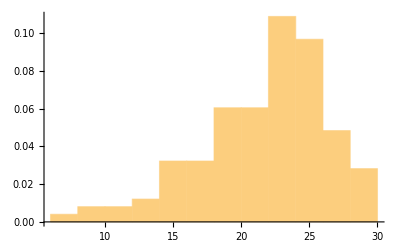

```mathematica
hist=Histogram[tempsChicago,Automatic,PDF]
```

Fit the distribution to PERTDistributionpaclet:ref/PERTDistribution:

```mathematica
dist=EstimatedDistribution[tempsChicago,PERTDistribution[{min,max},med,λ]]
```

QuantityDistribution[PERTDistribution[{-6.2638,29.18},24.5796,7.06168], °C]

Check goodness of fit:

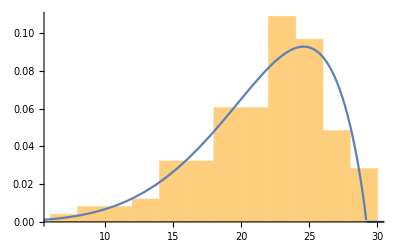

```mathematica
Show[hist,Plot[PDF[dist,Quantity[t,"Celsius"]]//Evaluate,{t,-7,32}]]
```

Find the estimated distribution for temperature in degrees Fahrenheit:

```mathematica
UnitConvert[dist,"DegreesFahrenheit"]
```

QuantityDistribution[PERTDistribution[{20.7252,84.5241},76.2432,7.06168], °F]

```mathematica
SIConstantConvert[dist]
```

QuantityDistribution::unkunit: Unable to interpret unit specification 1.

UnitConvert[QuantityDistribution[PERTDistribution[{-6.2638,29.18},24.5796,7.06168], °C],1 Δν(^133Cs)_hfs h/k]

```mathematica
QuantityUnit[dist]
```

DegreesCelsius

```mathematica
Quantity[QuantityUnit[dist]]
```

1 °C

```mathematica
SIConstantConvert[Quantity[QuantityUnit[dist]]]
```

75700984670000000000/121822045942277331 Δν(^133Cs)_hfs h/k

```mathematica
QuantityUnit[SIConstantConvert[Quantity[QuantityUnit[dist]]]]
```

(Cesium133HyperfineSplittingFrequency PlanckConstant)/BoltzmannConstant

```mathematica
Quantity[QuantityUnit[SIConstantConvert[Quantity[QuantityUnit[dist]]]]]
```

1 Δν(^133Cs)_hfs h/k

```mathematica
TransformedDistribution[Quantity[x,Quantity[QuantityUnit[SIConstantConvert[Quantity[QuantityUnit[dist]]]]]],x\[Distributed]dist]
```

TransformedDistribution[Quantity[x,1 Δν(^133Cs)_hfs h/k],x\[Distributed]QuantityDistribution[PERTDistribution[{-6.2638,29.18},24.5796,7.06168], °C]]

```mathematica
Moment[TransformedDistribution[Quantity[x,Quantity[QuantityUnit[SIConstantConvert[Quantity[QuantityUnit[dist]]]]]],x\[Distributed]dist]]
```

Moment[TransformedDistribution[Quantity[x,1 Δν(^133Cs)_hfs h/k],x\[Distributed]QuantityDistribution[PERTDistribution[{-6.2638,29.18},24.5796,7.06168], °C]]]

```mathematica
TransformedDistribution[Quantity[x,"Meters"],x\[Distributed]LogNormalDistribution[μ,σ]]
```

```mathematica
TransformedDistribution[Quantity[x,QuantityUnit[SIConstantConvert[Quantity[QuantityUnit[dist]]]]],x\[Distributed]LogNormalDistribution[μ,σ]]
```

QuantityDistribution[LogNormalDistribution[μ,σ], Δν(^133Cs)_hfs h/k]

```mathematica
TransformedDistribution[Quantity[x,QuantityUnit[SIConstantConvert[Quantity[QuantityUnit[dist]]]]],x\[Distributed]dist]
```

QuantityDistribution[PERTDistribution[{-6.2638,29.18},24.5796,7.06168], Δν(^133Cs)_hfs °C h/k]

```mathematica
Moment[TransformedDistribution[Quantity[x,QuantityUnit[SIConstantConvert[Quantity[QuantityUnit[dist]]]]],x\[Distributed]dist]]
```

Moment[QuantityDistribution[PERTDistribution[{-6.2638,29.18},24.5796,7.06168], Δν(^133Cs)_hfs °C h/k]]

```mathematica
Mean[TransformedDistribution[Quantity[x,QuantityUnit[SIConstantConvert[Quantity[QuantityUnit[dist]]]]],x\[Distributed]dist]]
```

21.6835 Δν(^133Cs)_hfs °C h/k

```mathematica
QuantityUnit[Mean[TransformedDistribution[Quantity[x,QuantityUnit[SIConstantConvert[Quantity[QuantityUnit[dist]]]]],x\[Distributed]dist]]]
```

(Cesium133HyperfineSplittingFrequency DegreesCelsius PlanckConstant)/BoltzmannConstant

```mathematica
UnitDimensions["DegreesCelsius"]
```

{{TemperatureUnit,1}}

```mathematica
SIConstantConvert[Quantity["DegreesCelsius"]]
```

75700984670000000000/121822045942277331 Δν(^133Cs)_hfs h/k

```mathematica
Quantity[x,QuantityUnit[SIConstantConvert[Quantity[QuantityUnit[dist]]]]]
```

x Δν(^133Cs)_hfs h/k

### Neat Examples

Symbol names from above will not be defined here. Each example needs to work independently.

Convert all instances of physical quantities in the SI Brochure to products of constants:

```mathematica
SIBrochurePhysicalUnits=<|"time"->Quantity[1, "Seconds"],"length"->Quantity[1, "Meters"],"mass"->Quantity[1, "Kilograms"],"electric-current"->Quantity[1, "Amperes"],"thermodynamic-temperature"->Quantity[1, "Kelvins"],"amount-of-substance"->Quantity[1, "Moles"],"luminous-intensity"->Quantity[1, "Candelas"],"area"->Quantity[1, "Meters"],"volume"->Quantity[1, "Meters"],"speed-velocity"->Quantity[1, ("Meters")/("Seconds")],"acceleration"->Quantity[1, ("Meters")/("Seconds")],"wavenumber"->Quantity[1, "Meters"],"density-mass-density"->Quantity[1, ("Kilograms")/("Meters")],"surface-density"->Quantity[1, "Kilograms" "Meters"],"specific-volume"->Quantity[1, "Kilograms" "Meters"],"current-density"->Quantity[1, "Amperes" "Meters"],"magnetic-field-strength"->Quantity[1, "Amperes" "Meters"],"amount-of-substance-concentration"->Quantity[1, "Meters" "Moles"],"mass-concentration"->Quantity[1, "Kilograms" "Meters"],"luminance"->Quantity[1, "Candelas" "Meters"],"dynamic-viscosity"->Quantity[, "Pascals" "Seconds"],"moment-of-force"->Quantity[, "Meters" "Newtons"],"surface-tension"->Quantity[, ("Newtons")/("Meters")],"angular-velocity-angular-frequency"->Quantity[1, ("Radians")/("Seconds")],"angular-acceleration"->Quantity[1, ("Radians")/("Seconds")^2],"heat-flux-density-irradiance"->Quantity[1, ("Watts")/("Meters")^2],"heat-capacity-entropy"->Quantity[1, ("Joules")/("Kelvins")],"specific-heat-capacity-specific-entropy"->Quantity[1, ("Joules")/("Kelvins" "Kilograms")],"specific-energy"->Quantity[1, ("Joules")/("Kilograms")],"thermal-conductivity"->Quantity[1, ("Watts")/("Kelvins" "Meters")],"energy-density"->Quantity[1, ("Joules")/("Meters")^3],"electric-field-strength"->Quantity[1, ("Volts")/("Meters")],"electric-charge-density"->Quantity[1, ("Coulombs")/("Meters")^3],"surface-charge-density"->Quantity[1, ("Coulombs")/("Meters")^2],"electric-flux-density"->Quantity[1, ("Coulombs")/("Meters")^2],"permittivity"->Quantity[1, ("Farads")/("Meters")],"permeability"->Quantity[1, ("Henries")/("Meters")],"molar-energy"->Quantity[1, ("Joules")/("Moles")],"molar-entropy-molar-heat-capacity"->Quantity[1, ("Joules")/("Kelvins" "Moles")],"exposure-x-ray-γ-ray"->Quantity[1, ("Coulombs")/("Kilograms")],"absorbed-dose-rate"->Quantity[1, ("Grays")/("Seconds")],"radiant-intensity"->Quantity[1, ("Watts")/("Steradians")],"radiance"->Quantity[1, ("Watts")/(("Meters")^2 "Steradians")],"catalytic-activity-concentration"->Quantity[1, ("Katals")/("Meters")^3]|>;
```

```mathematica
{#,SIConstantConvert[#],N[SIConstantConvert[#]]}&/@SIBrochurePhysicalUnits
```

<|time→{1 s,9192631770 /Δν(^133Cs)_hfs,9.19263×10^9 /Δν(^133Cs)_hfs},length→{1 m,656616555/21413747 c/Δν(^133Cs)_hfs,30.6633 c/Δν(^133Cs)_hfs},mass→{1 kg,36683884846400720000000000000000000000000000000000000000/2486164202903619 Δν(^133Cs)_hfs h/c^2,1.47552×10^40 Δν(^133Cs)_hfs h/c^2},electric-current→{1 A,500000000000000000000000000/736410991343003109 Δν(^133Cs)_hfs e,6.78969×10^8 Δν(^133Cs)_hfs e},thermodynamic-temperature→{1 K,276129800000000000/121822045942277331 Δν(^133Cs)_hfs h/k,2.26667 Δν(^133Cs)_hfs h/k},amount-of-substance→{1 mol,602214076000000000000000 /N_A,6.02214×10^23 /N_A},luminous-intensity→{1 cd,2000000000000000000000000000000000000000/76486793830390329632626020921 (Δν(^133Cs)_hfs)^2 K_cd h/rad^2,2.61483×10^10 (Δν(^133Cs)_hfs)^2 K_cd h/rad^2},area→{1 m,656616555/21413747 c/Δν(^133Cs)_hfs,30.6633 c/Δν(^133Cs)_hfs},volume→{1 m,656616555/21413747 c/Δν(^133Cs)_hfs,30.6633 c/Δν(^133Cs)_hfs},speed-velocity→{1 m/s,1/299792458 c,3.33564×10^-9 c},acceleration→{1 m/s,1/299792458 c,3.33564×10^-9 c},wavenumber→{1 m,656616555/21413747 c/Δν(^133Cs)_hfs,30.6633 c/Δν(^133Cs)_hfs},density-mass-density→{1 kg/m,157107885815591775739568000000000000000000000000000000000000000/326491314814979060962509 (Δν(^133Cs)_hfs)^2 h/c^3,4.81201×10^38 (Δν(^133Cs)_hfs)^2 h/c^3},surface-density→{1 kg m,8565498800000000000000000000000000000000000000000/18931629 h/c,4.52444×10^41 h/c},specific-volume→{1 kg m,8565498800000000000000000000000000000000000000000/18931629 h/c,4.52444×10^41 h/c},current-density→{1 m A,2500000000000000000000000000/120080117814256593 e c,2.08194×10^10 e c},magnetic-field-strength→{1 m A,2500000000000000000000000000/120080117814256593 e c,2.08194×10^10 e c},amount-of-substance-concentration→{1 m mol,395423731955628180000000000000000/21413747 c/(Δν(^133Cs)_hfs N_A),1.84659×10^25 c/(Δν(^133Cs)_hfs N_A)},mass-concentration→{1 kg m,8565498800000000000000000000000000000000000000000/18931629 h/c,4.52444×10^41 h/c},luminance→{1 m cd,10000000000000000000000000000000000000000/12472034397039680411344917717 Δν(^133Cs)_hfs K_cd h c/rad^2,8.01794×10^11 Δν(^133Cs)_hfs K_cd h c/rad^2},dynamic-viscosity→{1 s Pa,15710788581559177573956800000000000000000000000000000000000000/300131443319724818768872701231093 (Δν(^133Cs)_hfs)^3 h/c^3,5.23464×10^28 (Δν(^133Cs)_hfs)^3 h/c^3},moment-of-force→{1 m N,20000000000000000000000000000000000000000/121822045942277331 Δν(^133Cs)_hfs h,1.64174×10^23 Δν(^133Cs)_hfs h},surface-tension→{1 N/m,366838848464007200000000000000000000000000000000000000/2100920103238073731382108908617651 (Δν(^133Cs)_hfs)^3 h/c^2,1.74609×10^20 (Δν(^133Cs)_hfs)^3 h/c^2},angular-velocity-angular-frequency→{1 rad/s,1/9192631770 Δν(^133Cs)_hfs,1.08783×10^-10 Δν(^133Cs)_hfs},angular-acceleration→{1 rad/s^2,1/84504478858813332900 (Δν(^133Cs)_hfs)^2,1.18337×10^-20 (Δν(^133Cs)_hfs)^2},heat-flux-density-irradiance→{1 W/m^2,36683884846400720000000000000000000000000000000000000/1931298488725799645670562036295864536537227 (Δν(^133Cs)_hfs)^4 h/c^2,1.89944×10^10 (Δν(^133Cs)_hfs)^4 h/c^2},heat-capacity-entropy→{1 J/K,100000000000000000000000000000/1380649 k,7.24297×10^22 k},specific-heat-capacity-specific-entropy→{1 J/(kg K),2486164202903619/506475689292983076672800000000000 k c^2/(Δν(^133Cs)_hfs h),4.90875×10^-18 k c^2/(Δν(^133Cs)_hfs h)},specific-energy→{1 J/kg,1/89875517873681764 c^2,1.11265×10^-17 c^2},thermal-conductivity→{1 W/(m K),586678000000000000000000000000000/2283190298081052235911 (Δν(^133Cs)_hfs)^2 k/c,2.56955×10^11 (Δν(^133Cs)_hfs)^2 k/c},energy-density→{1 J/m^3,1571078858155917757395680000000000000000000000000000000000000/275899784103685663667223148042266362362461 (Δν(^133Cs)_hfs)^4 h/c^3,5.69438×10^18 (Δν(^133Cs)_hfs)^4 h/c^3},electric-field-strength→{1 V/m,1524826892879448800000000000/1777563825103774887462549 (Δν(^133Cs)_hfs)^2 h/(e c),857.818 (Δν(^133Cs)_hfs)^2 h/(e c)},electric-charge-density→{1 C/m^3,392769714538979439348920000000000000000000000000/1814286502896284971950427088494227 (Δν(^133Cs)_hfs)^3 e/c^3,2.16487×10^14 (Δν(^133Cs)_hfs)^3 e/c^3},surface-charge-density→{1 C/m^2,91709712116001800000000000000000000000000/13815418519993643565310557 (Δν(^133Cs)_hfs)^2 e/c^2,6.63821×10^15 (Δν(^133Cs)_hfs)^2 e/c^2},electric-flux-density→{1 C/m^2,91709712116001800000000000000000000000000/13815418519993643565310557 (Δν(^133Cs)_hfs)^2 e/c^2,6.63821×10^15 (Δν(^133Cs)_hfs)^2 e/c^2},permittivity→{1 F/m,1655371547624107250000000000000/213914163877964163 e^2/(h c),7.73848×10^12 e^2/(h c)},permeability→{1 H/m,4580703784999263461548761/394408937500000000000 h/(e^2 c),11614.1 h/(e^2 c)},molar-energy→{1 J/mol,5000000000000000000000000/18340737708389523055977789 Δν(^133Cs)_hfs N_A h,0.272617 Δν(^133Cs)_hfs N_A h},molar-entropy-molar-heat-capacity→{1 J/(K mol),25000000000000/207861565453831 N_A k,0.120272 N_A k},exposure-x-ray-γ-ray→{1 C/kg,276240466989291/653045146058332362053072000000000000 e c^2/(Δν(^133Cs)_hfs h),4.23004×10^-22 e c^2/(Δν(^133Cs)_hfs h)},absorbed-dose-rate→{1 Gy/s,1/826192540950809830616042280 Δν(^133Cs)_hfs c^2,1.21037×10^-27 Δν(^133Cs)_hfs c^2},radiant-intensity→{1 W/sr,2000000000000000000000000000000000000000/111986520981537817910140587 (Δν(^133Cs)_hfs)^2 h,1.78593×10^13 (Δν(^133Cs)_hfs)^2 h},radiance→{1 W/(m^2 sr),36683884846400720000000000000000000000000000000000000/1931298488725799645670562036295864536537227 (Δν(^133Cs)_hfs)^4 h/c^2,1.89944×10^10 (Δν(^133Cs)_hfs)^4 h/c^2},catalytic-activity-concentration→{1 kat/m^3,4730629014437505381010157987958400000000000/2081926223673361378970785179826887 (Δν(^133Cs)_hfs)^4/(N_A c^3),2.27224×10^9 (Δν(^133Cs)_hfs)^4/(N_A c^3)}|>

Transform units with angles:

```mathematica
SIConstantConvert[Quantity["Candelas""Lumens" "Lux" "Radians""Steradians"]]
```

146735539385602880000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000/7716902576846583556171907702803477749472118367789010280295202539706752269185837910869777022989442383881 (Δν(^133Cs)_hfs)^8 K_cd^3 h^3/(rad^6 c^2)

## Source & Additional Information

### Contributed By

Peter Cullen Burbery

### Keywords

Measurement

2019 SI revision

SI defining constants

Dimensional analysis

SI

International System of Units

Metrology

NIST

BIPM

units

### Categories

|

### Related Symbols

Quantity

QuantityDistribution

UnitSimplify

UnityDimensions

UnitDimensions

QuantityVariableDimensions

DimensionalCombinations

NondimensionalizationTransform

### Related Resource Objects

PlanckUnitConversion

StoneyUnitConversion

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.1+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

I would like to add support for QuantityDistribution but SIConstantConvert does not work with QuantityDistribution like UnitConvert does unfortunately.

## Submission Notes

I fixed some bugs with units related to angles, including { "cd", "rad", "sr", "lm", "lx",Quantity["MonochromaticRadiation540THzLuminousEfficacy"]}. There were $Failure output but now the function works for all these angle units.